# Code for model used in submission to Frontiers in Physics Containment of COVID-19

```mathematica
date=DateString[{"Day","Month","YearShort"}]
```

281020

```mathematica
filepath="/Users/mirjam/Projects/Corona/SocDistManuscript/SocDist2/Figures/";
```

```mathematica
AspRat=0.75;
ImSize=400;
```

## Model Parameters

## Biological parameters

```mathematica
meanhouseholdcontacts=2.15;negbinn=2.0;negbinp=0.15;
```

duration of the latent and infectious periods, casefatality, and ratio of transmission probabilities in 2. ring to 1. ring contacts:

```mathematica
latent=3;infectious=10;casefatality=0.02; 
transratio=0.25; 
transmissibility=0.152;
scenariocontactred={1.0,0.95,0.9,0.85,0.8,0.75,0.7,0.65,0.6,0.55,0.5,0.45,0.4,0.35,0.3,0.25,0.2,0.15,0.1,0.05};fractiontrace=1.0;fractest=1.0;
```

```mathematica
contactreduction1=scenariocontactred[[1]]
```

1.

```mathematica
contactreduction2=scenariocontactred[[1]]
```

1.

probability of leaving latent stage by time since infection:

```mathematica
probinf=Array[f,latent];
probinf=Flatten[Append[Table[0.0,{i,1,latent-3}],{0.5,0.7,1.0}]]
```

{0.5,0.7,1.}

```mathematica
startinf=Table[Product[(1-probinf[[k-1]]),{k,2,j}]*probinf[[j]],{j,1,latent}]
```

{0.5,0.35,0.15}

probability of transmission per contact by time since beginning of infectious period:

```mathematica
probtransm[pt_]=pt*{0.2588669601975381,0.39590915946603245,0.5193372549221815,0.5896863951059722,0.5845147775405406,0.5098095242416707,0.394158153684336,0.27201172443208405,0.16864247152434894,0.09449937156036968}
```

{0.258867 pt,0.395909 pt,0.519337 pt,0.589686 pt,0.584515 pt,0.50981 pt,0.394158 pt,0.272012 pt,0.168642 pt,0.0944994 pt}

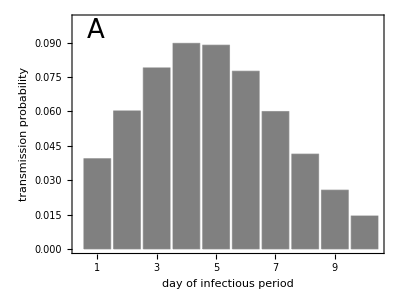

```mathematica
figure1a=Show[BarChart[probtransm[transmissibility],AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{All,{0.0,0.1}},ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17],FrameLabel->{"day of infectious period", "transmission probability"}],Graphics[Text[StyleForm["A",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,0.1*0.95}]]]
```

probability of developing symptoms by time since becoming infectious:

```mathematica
probsympdata=Table[PDF[LogNormalDistribution[1.434065,0.6612],x]/CDF[LogNormalDistribution[1.434065,0.6612],11],{x,1,10}]
```

{0.0619119,0.1736,0.190648,0.1622,0.125603,0.0936579,0.0688685,0.0504983,0.0371298,0.0274521}

```mathematica
Total[probsympdata]
```

0.99157

```mathematica
scenarioasymptomatictable={0.99,0.975,0.95,0.925,0.9,0.875,0.85,0.825,0.8,0.775,0.75,0.725,0.7,0.675,0.65,0.625,0.6,0.575,0.55,0.525,0.5,0.4,0.3,0.2,0.1};
```

```mathematica
calcsymp[x_]=Total[Table[Product[(1-x*probsympdata[[j-1]]),{j,2,i}]*x*probsympdata[[i]],{i,1,infectious}]];
scenarioasymptomatic=Table[FindRoot[calcsymp[x]==scenarioasymptomatictable[[i]],{x,0.5}],{i,1,Length[scenarioasymptomatictable]}][[All,1,2]];
```

```mathematica
scenarioasymptomatic
```

{3.40086,2.90148,2.47046,2.19573,1.99025,1.82467,1.68528,1.5645,1.45767,1.36173,1.27453,1.19451,1.12052,1.05165,0.987189,0.926579,0.869354,0.815131,0.76359,0.714462,0.667516,0.497954,0.351276,0.221728,0.105515}

```mathematica
factorasymptomatic=scenarioasymptomatic[[9]];
```

```mathematica
probsymp=factorasymptomatic*probsympdata
```

{0.0902472,0.253052,0.277902,0.236435,0.183088,0.136523,0.100388,0.07361,0.054123,0.0400162}

```mathematica
probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];
```

```mathematica
fraccas=Total[probdevelopingsymptoms]
```

0.8

```mathematica
Mean[LogNormalDistribution[1.434065,0.6612]]//N
```

5.22084

```mathematica
Median[LogNormalDistribution[1.434065,0.6612]]//N
```

4.19572

```mathematica
StandardDeviation[LogNormalDistribution[1.434065,0.6612]]//N
```

3.86604

```mathematica
plotlognormal=Plot[PDF[LogNormalDistribution[1.434065,0.6612],x],{x,0,13}];
```

```mathematica
CDF[LogNormalDistribution[1.434065,0.6612],10]
```

0.905501

```mathematica
plotlognormalcdf=Plot[CDF[LogNormalDistribution[1.434065,0.6612],x],{x,0,13},PlotRange->{All,{0,1}},GridLines->{None,{CDF[LogNormalDistribution[1.434065,0.6612],13],1}}];
```

```mathematica
plotincubation=ListPlot[Total[Table[PadRight[startinf[[k]]*PadLeft[probdevelopingsymptoms,infectious+k-1],infectious+latent],{k,1,latent}]],PlotMarkers->"OpenMarkers",PlotStyle->Red];
```

```mathematica
Table[PadRight[startinf[[k]]*PadLeft[probdevelopingsymptoms,infectious+k],infectious+latent],{k,1,latent}];
```

```mathematica
plotincubation2=BarChart[Total[Table[PadRight[startinf[[k]]*PadLeft[probdevelopingsymptoms,infectious+k-1],infectious+latent],{k,1,latent}]],Frame->True,ChartLabels->Table[i,{i,1,infectious+latent}],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious+latent}],None}}, FrameStyle->Directive[Black,17], FrameLabel->{"day since infection", "probability symptoms"}];
```

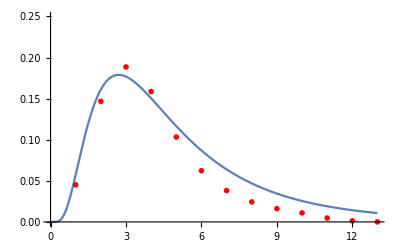

```mathematica
Show[plotlognormal,plotincubation,PlotRange->{All,{0,0.25}}]
```

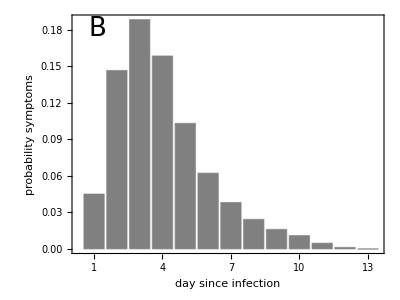

```mathematica
figure1b=Show[plotincubation2,Graphics[Text[StyleForm["B",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(12.0-0.5)*0.1,0.19*0.95}]]]
```

```mathematica
plotprobsymptoms=BarChart[probdevelopingsymptoms, Frame->True,ChartLabels->Table[i,{i,1,infectious}],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True, FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}, FrameStyle->Directive[Black,17], FrameLabel->{"day of infectious period", "probability symptoms"}];
```

distribution of the number of contacts with susceptibles by time since beginning of the infectious period:

```mathematica
saturation1=Drop[Prepend[Table[Product[1-probtransm[transmissibility][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.960652,0.902842,0.831572,0.757036,0.689777,0.636325,0.598202,0.573468,0.558768}

```mathematica
saturation2=Drop[Prepend[Table[Product[1-probtransm[transmissibility*transratio][[j]],{j,1,i}],{i,1,infectious}],1.0],-1]
```

{1.,0.990163,0.975266,0.95602,0.934597,0.913838,0.896135,0.882712,0.873588,0.86799}

```mathematica
BarChart[saturation1,ChartLabels->Table[i,{i,1,infectious}]];
```

```mathematica
mu1=meanhouseholdcontacts*saturation1*contactreduction1
```

{2.15,2.0654,1.94111,1.78788,1.62763,1.48302,1.3681,1.28613,1.23296,1.20135}

```mathematica
mu2=negbinn*saturation2*contactreduction2
```

{2.,1.98033,1.95053,1.91204,1.86919,1.82768,1.79227,1.76542,1.74718,1.73598}

```mathematica
contactdist1=Array[f,infectious];contactdist2=Array[f,infectious];
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];
```

```mathematica
contact=Array[f,latent+infectious];
For [i=1,i≤infectious,i++,contact[[i]]=Mean[contactdist1[[i]]]+Mean[contactdist2[[i]]]]
```

```mathematica
numcontacts=Table[RandomVariate[contactdist1[[i]],1000]+RandomVariate[contactdist2[[i]],1000],{i,1,infectious}];
```

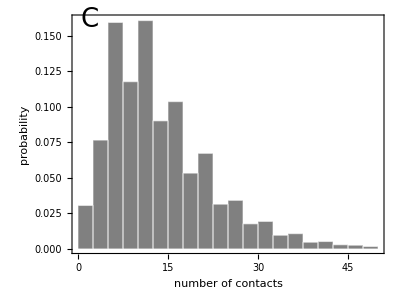

```mathematica
figure1c=Show[Histogram[RandomVariate[PoissonDistribution[meanhouseholdcontacts*contactreduction1],10000]+RandomVariate[NegativeBinomialDistribution[negbinn*contactreduction2,negbinp],10000], {0, 50, 2.5},"Probability", ChartBaseStyle->EdgeForm[White],AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"number of contacts", "probability"},FrameTicks->{{True,None},{True,None}}],Graphics[Text[StyleForm["C",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{2.0,0.17*0.95}]]]
```

```mathematica
meancontacts=Table[Mean[numcontacts[[i]]],{i,1,infectious}]//N
```

{13.461,13.033,12.961,12.897,12.417,11.58,11.374,11.413,11.148,10.67}

```mathematica
plotmeancontacts=BarChart[meancontacts, ChartLabels->Table[i,{i,1,infectious}],AxesLabel->{"day infectious period","mean number of contacts with susceptibles"}];
```

```mathematica
stdcontacts=Table[StandardDeviation[numcontacts[[i]]],{i,1,infectious}]//N
```

{8.79283,8.51531,8.64316,8.86685,8.82978,8.19052,8.39956,8.3836,7.98435,7.487}

```mathematica
ListPlot[stdcontacts];
```

basic reproduction ratio:

```mathematica
rzero[pt_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])
```

```mathematica
Plot[rzero[x],{x,0,0.2},GridLines->{None,{2.5}}];
```

```mathematica
rzero1[pt_]:=∑_(i=1)^infectious Mean[contactdist1[[i]]]*probtransm[pt][[i]]
```

```mathematica
rzero2[pt_, tr_]:=∑_(i=1)^infectious Mean[contactdist2[[i]]]*probtransm[tr*pt][[i]]
```

```mathematica
rzero1[transmissibility]
```

0.965904

```mathematica
rzero2[transmissibility, transratio]
```

1.53144

```mathematica
rzero1[transmissibility]+rzero2[transmissibility,transratio]
```

2.49734

```mathematica
ratiohousehold[pt_, tr_]:=rzero1[pt]/(rzero1[pt]+rzero2[pt,tr]);
```

```mathematica
ratiohousehold[transmissibility, transratio]
```

0.386773

```mathematica
rzeroday[pt_]:=Table[Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[pt][[i]]*transratio, {i,1,infectious}]
```

```mathematica
rzeroperc=rzeroday[transmissibility]/rzero[transmissibility]*100
```

{7.85167,11.7373,14.8702,16.1388,15.2112,12.6359,9.37337,6.26998,3.80616,2.10549}

```mathematica
rzerocum=Table[∑_(i=1)^j rzeroperc[[i]], {j,1,infectious}];
```

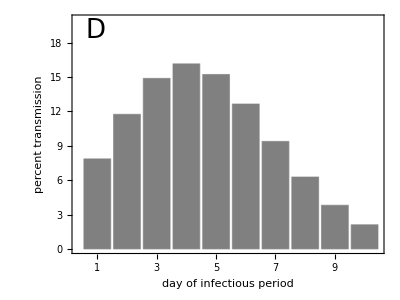

```mathematica
figure1d=Show[BarChart[rzeroperc,  AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],PlotRange->{All,{0,20}},Frame->True, FrameLabel->{"day of infectious period", "percent transmission"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["D",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,20*0.95}]]]
```

```mathematica
rzerodaysinceinf[pt_]:=Total[Table[PadRight[startinf[[k]]*PadLeft[Table[Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[pt][[i]]*transratio, {i,1,infectious}],infectious+k-1],infectious+latent],{k,1,latent}]]
```

```mathematica
rzeropercsinceinf=rzerodaysinceinf[transmissibility]/rzero[transmissibility]*100
```

{3.92584,8.61672,12.7209,15.0346,15.4847,14.0627,11.3909,8.31105,5.50358,3.3254,1.30785,0.315824,0.}

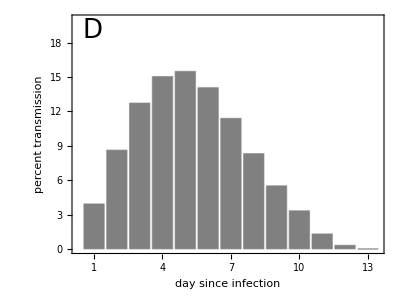

```mathematica
figure1d2=Show[BarChart[rzeropercsinceinf,  AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5],PlotRange->{All,{0,20}},Frame->True, FrameLabel->{"day since infection", "percent transmission"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious+latent}],None}}],Graphics[Text[StyleForm["D",FontSize->26(*, FontWeight->"Bold",FontColor-> Black*)],{(10.0-0.5)*0.1,20*0.95}]]]
```

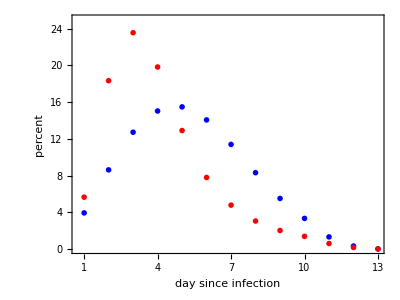

```mathematica
figure1d3=ListPlot[{rzeropercsinceinf,Total[Table[PadRight[startinf[[k]]*PadLeft[probdevelopingsymptoms,infectious+k-1],infectious+latent],{k,1,latent}]]/Total[Total[Table[PadRight[startinf[[k]]*PadLeft[probdevelopingsymptoms,infectious+k-1],infectious+latent],{k,1,latent}]]]*100},PlotMarkers->"OpenMarkers",PlotStyle->{Blue,Red},PlotRange->{All,{0,25}},AspectRatio->AspRat,ImageSize->ImSize,Frame->True, FrameLabel->{"day since infection", "percent"},FrameStyle->Directive[Black,17],  FrameTicks->{{True,None},{Table[i,{i,1,infectious+latent}],None}}]
```

## Individual reproduction number

```mathematica
rzeroindiv[pt_]:= Sum[RandomVariate[BinomialDistribution[RandomVariate[contactdist1[[i]]],probtransm[pt][[i]]]]+RandomVariate[BinomialDistribution[RandomVariate[contactdist2[[i]]],probtransm[transratio*pt][[i]]]],{i,1,infectious}];
```

```mathematica
ListPlot[Table[{transmissibility*i,Around[Table[rzeroindiv[transmissibility*i],{k,1,100}]]},{i,1,3}],IntervalMarkers->"Bands",IntervalMarkersStyle->Directive[Gray,Thickness[0.002]],Joined->True];
```

## Exponential growth rate and doubling time

```mathematica
generations[r_,pt_]:=Sum[Sum[Exp[-r*(i+j)]*startinf[[j]](Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]),{i,1,infectious}],{j,1,latent}]
```

```mathematica
expgrowth[pt_]:=FindRoot[generations[r,pt]==1,{r,1}][[1,2]]
```

```mathematica
unconstrainedgrowth=expgrowth[transmissibility]
```

0.156161

```mathematica
doublingtime[pt_]:=Log[2]/expgrowth[pt];
```

```mathematica
unconstraineddoubtime=doublingtime[transmissibility]
```

4.43867

## Definition of vaccination and quarantine parameters

```mathematica
timewindow=7;
```

probability of being diagnosed by day since first symptoms for the first index case:

```mathematica
probdiag:=Table[Table[If[i<ds ,0.0,fractest*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
probdiag[[1]]
```

{0.0902472,0.253052,0.277902,0.236435,0.183088,0.136523,0.100388,0.07361,0.054123,0.0400162}

```mathematica
probbeingdiagnosed=Table[Table[Product[(1-probdiag[[ds,j-1]]),{j,2,i}]*probdiag[[ds,i]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
Total[Transpose[probbeingdiagnosed]][[1]]
```

0.8

```mathematica
probdiagtest[fa_]=Table[Table[If[i<ds ,0.0,fa*probsymp[[i-ds+1]]],{i,1,infectious}],{ds,1,infectious}];
```

```mathematica
cumprobbeingdiagnosed=Table[Table[Sum[probbeingdiagnosed[[j,k]],{k,1,i}],{i,1,infectious}],{j,1,infectious}];
```

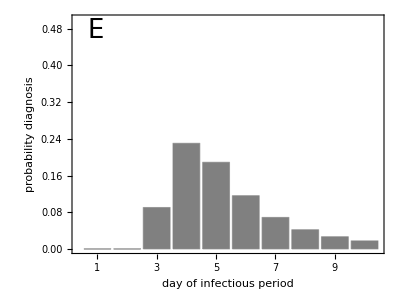

```mathematica
figure1e=Show[BarChart[probbeingdiagnosed[[3]], PlotRange->{All,{0,0.5}}, AspectRatio->AspRat,ImageSize->ImSize,ChartStyle->GrayLevel[0.5], FrameStyle->Directive[Black,17],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{{True,None},{Table[i,{i,1,infectious}],None}}],Graphics[Text[StyleForm["E",FontSize->26],{(10.0-0.5)*0.1,0.5*0.95}]]]
```

contact tracing and vaccination:

probability of being diagnosed on day i, if one has not been diagnosed up to day j (i>j):

```mathematica
pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
sums=Table[∑_(k=1)^(infectious-j) pd[[1,j,k]],{j,1,infectious-1}]
```

{0.78016,0.705682,0.592413,0.466205,0.34657,0.243258,0.158813,0.0919734,0.0400162}

```mathematica
BarChart[sums, ChartStyle->{GrayLevel[0.8]},ChartLabels->Table[i,{i,1,infectious}],Frame->True, FrameLabel->{"day of infectious period", "probability diagnosis"},FrameTicks->{Automatic,Automatic,None,None}];
```

```mathematica
rzerodayprob=rzeroday[transmissibility]/rzero[transmissibility]
```

{0.0785167,0.117373,0.148702,0.161388,0.152112,0.126359,0.0937337,0.0626998,0.0380616,0.0210549}

```mathematica
cumrzerodayprob=Table[Sum[rzerodayprob[[j]],{j,1,i}],{i,1,infectious}]
```

{0.0785167,0.195889,0.344591,0.505979,0.658091,0.78445,0.878184,0.940884,0.978945,1.}

```mathematica
transmissionweights=PadRight[1-Total[Table[startinf[[k]]*PadLeft[Drop[cumrzerodayprob,-k],infectious],{k,1,latent}]],infectious+timewindow]
```

{1.,0.960742,0.874574,0.747366,0.59702,0.442173,0.301546,0.187637,0.104526,0.0494907,0,0,0,0,0,0,0}

probability of a contact being isolated by day since first symptoms of source (probtrace2: source is secondary case, contact is ring 1; probtrace3: source is secondary case, contact is ring 2):

```mathematica
probtrace[vd_,cv_,fa_]:=fa*Table[Flatten[{Table[∑_(j=i)^Min[i-1+Length[pd[[ds,i]]],i+timewindow] pd[[ds,i,j-i+1]]*cv*transmissionweights[[j+vd-1]],{i,1,infectious-1}],0}],{ds,1,infectious}];
```

```mathematica
ListPlot[probtrace[1,1,1],Joined->True];
```

effective reproduction ratio with diagnosis probability  as above for all infecteds:

```mathematica
reffiso[pt_,ds_]:=∑_(i=1)^infectious ((Mean[contactdist1[[i]]]*probtransm[pt][[i]]+Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

effective reproduction ratio with contact tracing:

```mathematica
reffvacc1[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious (Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc2[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious ( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))
```

```mathematica
reffvacc[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=reffvacc1[pt,vd1,vd2,cv1,cv2,ds,fa]+reffvacc2[pt,vd1,vd2,cv1,cv2,ds,fa]
```

## Exponential growth rate and doubling time

```mathematica
generationseff[r_,pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=∑_(i=1)^infectious Sum[Exp[-r*(i+k)]*startinf[[k]]*((Mean[contactdist1[[i]]]*probtransm[pt][[i]]*(1-probtrace[vd1,cv1,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))+( Mean[contactdist2[[i]]]*probtransm[transratio*pt][[i]]*(1-probtrace[vd2,cv2,fa][[ds,i]])*∏_(j=1)^(i-1) (1-probdiag[[ds,j]]))),{k,1,latent}];
```

```mathematica
expgrowtheff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=FindRoot[generationseff[r,pt,vd1,vd2,cv1,cv2,ds,fa]==1,{r,1}][[1,2]]
```

```mathematica
doublingtimeeff[pt_,vd1_,vd2_,cv1_,cv2_,ds_,fa_]:=Log[2]/expgrowtheff[pt,vd1,vd2,cv1,cv2,ds,fa];
```

## Specific parameter values

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=1.0; coverage3=1.0;diagdelay=1;
```

```mathematica
reffiso[transmissibility,diagdelay]
```

1.28277

```mathematica
doubeffiso=doublingtimeeff[transmissibility,5,5,0,0,diagdelay,fractiontrace]
```

14.2531

```mathematica
reffvacc1[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractiontrace]
```

0.321139

```mathematica
reffvacc2[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractiontrace]
```

0.497974

```mathematica
reffvacc[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractiontrace]
```

0.819113

```mathematica
expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractiontrace]
```

-0.0332764

```mathematica
doubeff=doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,diagdelay,fractiontrace]
```

-20.83

```mathematica
doubincrease=doubeff/unconstraineddoubtime
```

-4.69284

```mathematica
xdata=Table[rzero[pt],{pt,0,0.4,0.05}]
```

{0.,0.821494,1.64299,2.46448,3.28598,4.10747,4.92896,5.75046,6.57195}

```mathematica
ydata0=Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.1,diagdelay,fractiontrace],{pt,0,0.4,0.05}],{cv,1,11}];
```

```mathematica
figure1=Transpose[Prepend[ydata0,xdata]];
```

```mathematica
table[pairs_]:=TableForm[pairs, TableAlignments->Center]
```

```mathematica
legendr0=LineLegend[Table[RGBColor[1-(j-1)*0.2,0,0.5],{j,1,6}],Table[2*( j-1)*10,{j,1,6}],LegendLabel->"Tracing coverage (%)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table]
```

```mathematica
figure2a=Show[Show[Table[ListPlot[Transpose[{xdata,ydata0[[2*k-1]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize, PlotStyle->{RGBColor[1-(k-1)*0.2,0,0.5],Thickness[0.007]}],{k,1,6}], PlotRange->{{1,3},{0,1.5}}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},{{1,{Red,Thickness[0.007]}}}},  Frame->True, FrameLabel->{{ Text[Subscript[R,e]],None},{Text[Subscript[R,0]],None}},  FrameStyle->Directive[Black,17], FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["A",FontSize->26],{1.0+0.1,1.5*0.95}]]];
```

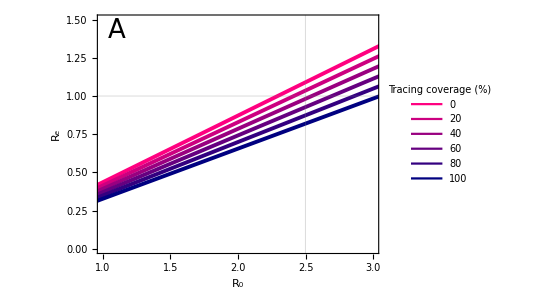

```mathematica
Show[Legended[figure2a,legendr0]]
```

```mathematica
ydata1=Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{pt,0,0.4,0.05}],{dd,1,10}];
```

```mathematica
figure2=Transpose[Prepend[ydata1,xdata]];
```

```mathematica
table2[pairs_]:=TableForm[pairs, TableAlignments->Center,TableDirections->"ReversedColumn"]
```

```mathematica
legendr02=LineLegend[Table[RGBColor[(j-1)*0.15,0,0.5],{j,1,7}],Table[j-1,{j,1,7}],LegendLabel->"Testing delay (days)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table2]
```

```mathematica
figure2b=Show[Show[Table[ListPlot[Transpose[{xdata,ydata1[[k]]}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[(k-1)*0.15,0,0.5],Thickness[0.007]} ],{k,1,7}], PlotRange->{{1,3},{0,2.5}}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},{{1,{Red,Thickness[0.007]}}}}, Frame->True,FrameStyle->Directive[Black,17], FrameLabel->{{ Text[Subscript[R,e]],None},{Text[Subscript[R,0]],None}},  FrameTicks->{Automatic, Automatic, None, None}], Graphics[Text[StyleForm["B",FontSize->26],{1.0+0.1,2.5*0.95}]]];
```

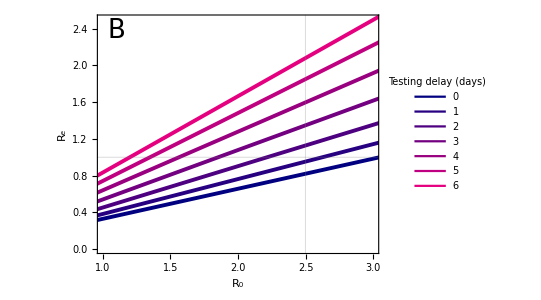

```mathematica
Show[Legended[figure2b,legendr02]]
```

```mathematica
xdata2=Table[rzero[pt],{pt,0.01,0.5,0.01}];
```

```mathematica
critcov2=Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,cv2,j,fractiontrace]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.01}],{j,1,7}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
figure3=Transpose[Prepend[critcov2,xdata2]];
```

```mathematica
figurecritcov1=Show[Table[ListPlot[Transpose[{xdata2,critcov2[[j]]}], Joined->True,PlotRange->{{0,3},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.4,0], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],Red}},None}],{j,1,7}], Frame->True,FrameLabel->{"R0", "fraction isolated"},  FrameTicks->{Automatic, Automatic, None, None},PlotLabel->"Varying time to diagnosis",FrameStyle->Directive["Label",16]];
```

```mathematica
xdata3=Table[rzero[pt],{pt,0.01,0.5,0.01}];
```

```mathematica
critcov3=Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,j,coverage2,cv2,3,fractiontrace]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.01}],{j,1,5}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
figure4=Transpose[Prepend[critcov3,xdata3]];
```

```mathematica
figurecritcov2=Show[Table[ListPlot[Transpose[{xdata3,critcov3[[j]]}], Joined->True,PlotRange->{{1,5},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.4,0], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],Red}},None}],{j,1,5}], Frame->True, FrameLabel->{"R0","fraction isolated"},FrameStyle->Directive["Label",16],FrameTicks->{Automatic, Automatic, None,None},PlotLabel->"Varying time to trace non-household contacts"];
```

## Scenarios asymptomatic infection

```mathematica
fractionsymptomatic={};ydata00={};ydata11={};critcov22={};critcov33={};growthrate={};doubtime={};
growthrate2={};
doubtime2={};
```

```mathematica
scenarios=Length[scenarioasymptomatic];
```

```mathematica
Do[
factorasymptomatic=scenarioasymptomatic[[l]]; 
 probsymp=factorasymptomatic*probsympdata;
probdevelopingsymptoms=Table[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],{i,1,infectious}];
fraccas=Total[probdevelopingsymptoms];
fractionsymptomatic=Append[fractionsymptomatic,fraccas];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
ydata00=Append[ydata00,Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,(cv-1)*0.1,(cv-1)*0.1,diagdelay,fractiontrace],{pt,0,0.4,0.05}],{cv,1,11}]];
ydata11=Append[ydata11,1Table[Table[reffvacc[pt,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{pt,0,0.4,0.05}],{dd,1,3}]];
critcov22=Append[critcov22,Table[Table[Part[FindRoot[reffvacc[pt,vaccdelay2,vaccdelay3,cv2,cv2,j,fractiontrace]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.01}],{j,1,10}]];
critcov33=Append[critcov33,Table[Table[Part[FindRoot[reffvacc[pt,j,j,cv2,cv2,diagdelay,fractiontrace]==1, {cv2,0.5}],1,2],{pt,0.01,0.5,0.01}],{j,1,7}]];
growthrate=Append[growthrate,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,10}]];
doubtime=Append[doubtime,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,10}]];
growthrate2=Append[growthrate2,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.1,(cv-1)*0.1,diagdelay,fractiontrace],{cv,1,11}]];
doubtime2=Append[doubtime2,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.1,(cv-1)*0.1,diagdelay,fractiontrace],{cv,1,11}]];,{l,Length[scenarioasymptomatic]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
fractionsymptomatic[[1]]
```

0.99

```mathematica
legendtextsymp=Table[ToString[NumberForm[100*fractionsymptomatic[[i]],{3,1}]],{i,1,Length[fractionsymptomatic]}]
```

{99.0,97.5,95.0,92.5,90.0,87.5,85.0,82.5,80.0,77.5,75.0,72.5,70.0,67.5,65.0,62.5,60.0,57.5,55.0,52.5,50.0,40.0,30.0,20.0,10.0}

```mathematica
ydata00;
```

```mathematica
ydata11;
```

```mathematica
critcov22 ;
```

```mathematica
Length[critcov33 [[1,1]]]
```

50

```mathematica
figurereff00=Show[Table[ListPlot[Transpose[{xdata,ydata00[[k,10]]}],Joined->True,PlotStyle->{RGBColor[k*0.1,0.4,0],Thickness[0.005]}],{k,1,scenarios}], PlotRange->{{0,5},{0,3}}, GridLines->{{rzero[transmissibility]},{{1,Red}}},Frame->True, FrameLabel->{"R0", "R_e"},  PlotLabel->"Varying proportion asymptomatic", FrameTicks->{Automatic, Automatic, None, None}, FrameStyle->Directive["Label",16]];
```

```mathematica
figurereff11=Show[Table[ListPlot[Transpose[{xdata,ydata11[[k,diagdelay]]}],Joined->True,PlotStyle->{RGBColor[k*0.1,0.4,0],Thickness[0.005]} ],{k,1,scenarios}], PlotRange->{{0,5},{0,3}}, GridLines->{{rzero[transmissibility]},{{1,Red}}}, Frame->True, FrameLabel->{"R0", "R_e"}, FrameTicks->{Automatic, Automatic, None, None},PlotLabel->"Varying proportion asymptomatic",FrameStyle->Directive["Label",16]];
```

```mathematica
figurecritcov22=Show[Table[ListPlot[Transpose[{xdata3,critcov22[[j,1]]}], Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotRange->{{0,5},{0,1.0}}, PlotStyle->{RGBColor[j 0.1,0.0,0.5], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,scenarios}], Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text[Fraction isolated],None},{Text[Subscript[R,0]],"Varying fraction asymptomatic"}},FrameTicks->{Automatic, Automatic, None,None} ];
```

```mathematica
scennumber={9,17};
```

```mathematica
graphlabels={ToString[A],ToString[C]};
```

```mathematica
graphlabels2={ToString[B],ToString[D]};
```

```mathematica
xlabels=Text[ Style[#,Large]]&/@{"Varying diagnosis delay","Varying tracing delay"};
ylabels=Text[Style[#,Large]]&/@Table[StringJoin[legendtextsymp[[scennumber[[k]]]],"% asymptomatic"],{k,1,2}];
```

```mathematica
legend2=LineLegend[Table[RGBColor[j*0.2,0,0.5],{j,1,5}],Table[ j-1,{j,1,5}],LegendLabel->"Testing delay (days)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table]
```

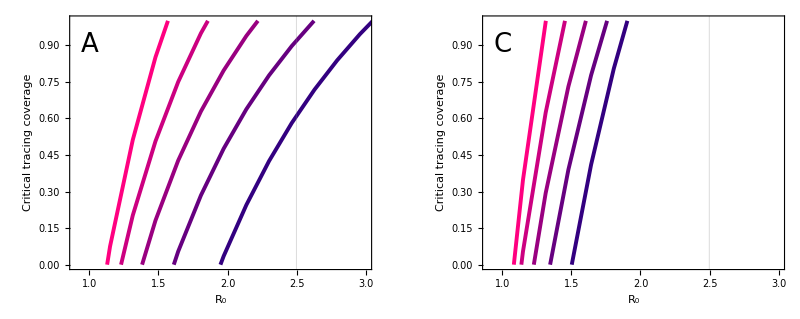

```mathematica
figure3firstpanel=Legended[GraphicsRow[Table[Show[Show[Table[ListPlot[Transpose[{xdata3,critcov22[[scennumber[[k]],j]]}], Joined->True,AspectRatio->AspRat, PlotRange->{{0.9,3},{0,1.0}}, PlotStyle->{RGBColor[j 0.2,0.0,0.5], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,5}],Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text["Critical tracing coverage"],None},{Text[Subscript[R,0]],StringJoin[(*"Varying testing delay, ",*) legendtextsymp[[scennumber[[k]]]],"% symptomatic"]}},FrameTicks->{Automatic, Automatic, None,None} ],Graphics[Text[StyleForm[graphlabels[[k]],FontSize->26],{1.0,1.0*0.9}]]],{k,1,2}],ImageSize->2*ImSize],legend2]
```

```mathematica
legend3=LineLegend[Table[RGBColor[j*0.2,0,0.5],{j,1,5}],Table[ j-1,{j,1,5}],LegendLabel->"Tracing delay (days)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table]
```

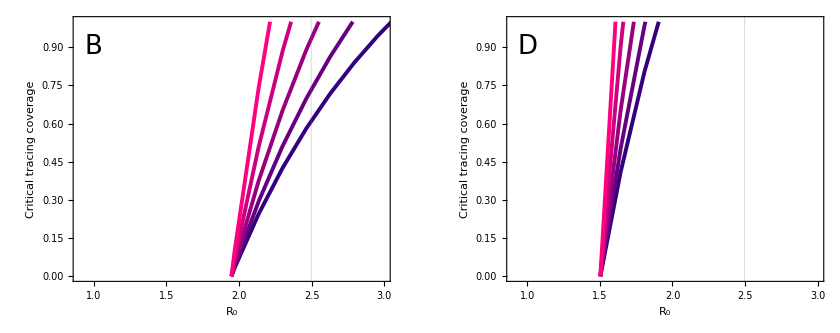

```mathematica
figure3secondpanel=Legended[GraphicsRow[Table[Show[Show[Table[ListPlot[Transpose[{xdata3,critcov33[[scennumber[[k]],j]]}], Joined->True,AspectRatio->AspRat, PlotRange->{{0.9,3},{0,1.0}}, PlotStyle->{RGBColor[j 0.2,0.0,0.5], Thickness[0.007]}, GridLines->{{{rzero[transmissibility],{Green,Thickness[0.007]}}},None}],{j,1,5}], Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{{ Text["Critical tracing coverage"],None},{Text[Subscript[R,0]],StringJoin[(*"Varying tracing delay, ",*) legendtextsymp[[scennumber[[k]]]],"% symptomatic"]}},FrameTicks->{Automatic, Automatic, None,None}  ],Graphics[Text[StyleForm[graphlabels2[[k]],FontSize->26],{1.0,1.0*0.9}]]],{k,1,2}],ImageSize->2.1*ImSize],legend3]
```

```mathematica
xdata3;
```

```mathematica
xvalue=Take[Flatten[Position[xdata3,SelectFirst [xdata3, #>rzero[transmissibility]&]]-1],1] [[1]]
```

15

```mathematica
xvalues=Table[Take[Flatten[Position[xdata3,SelectFirst [xdata3, #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}]
```

{9,12,15,18,21}

```mathematica
xdata3[[xvalues]]
```

{1.47869,1.97159,2.46448,2.95738,3.45028}

```mathematica
xdata3[[xvalue+1]]
```

2.62878

```mathematica
rzero[transmissibility]
```

2.49734

```mathematica
critcov33[[2,1,xvalue]]
```

-0.531893

```mathematica
coverages=Table[Table[{fractionsymptomatic[[j]],Max[-1.0,Min[2.0,critcov33[[j,1,xvalues[[k]]]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,scenarios}],{k,1,5}];
```

```mathematica
legendlabels=NumberForm[Table[1.0+0.5*k,{k,1,5}],{2,1}]
```

{1.5,2.0,2.5,3.0,3.5}

```mathematica
legend={LineLegend[ Table[RGBColor[k 0.2,0.0,0.5],{k,1,5}],coverages[[All,1,3]],LegendLabel->"R_0",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

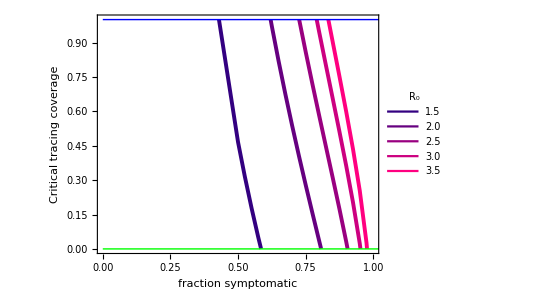

```mathematica
figure4a=Show[Show[Table[ListPlot[ Transpose[{Transpose[coverages[[k]]][[1]],Transpose[coverages[[k]]][[2]]}],Joined->True, (*Mesh->Full,*)PlotRange->{{0,1},{0,1.0}},PlotRangePadding->{None,0.05},AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, PlotLegends->Placed[legend[[k]],{0.15,0.4}], Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"fraction symptomatic","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]](*,Graphics[Text[StyleForm["A",FontSize->26],{0.95,1.0*0.95}]]*),Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]]
```

```mathematica
growthrate[[1,1]]
```

-0.348778

```mathematica
figexpgrowth=ListPlot[ Table[Table[{fractionsymptomatic[[j]],growthrate[[j,k]]},{j,1,scenarios}],{k,1,10}],PlotStyle->Table[{RGBColor[k 0.1,0.4,0], Thickness[0.007]},{k,1,10}],Joined->True, PlotRange->{{0.5,1.0},All},Frame->True,FrameLabel->{"fraction symptomatic","exponential growth rate"},PlotLabel->"Varying time to diagnosis"];
```

```mathematica
doubtime;
```

```mathematica
ListPlot[ Table[Table[{fractionsymptomatic[[j]],doubtime[[j,k]]},{j,1,scenarios}],{k,1,5}],PlotRange->{{0,1},{-20,100}},Joined->True,Mesh->Full,Frame->True,FrameLabel->{"fraction symptomatic","doubling time"}];
```

```mathematica
ydata11[[1,1,3]]
```

0.0848989

```mathematica
growthrate[[1]]
```

{-0.348778,-0.263241,-0.164636,-0.0737649,-0.000529114,0.0544235,0.0937864,0.121197,0.140437,0.152656}

```mathematica
Length[scenarios]
```

0

```mathematica
table[pairs_]:=TableForm[pairs, TableAlignments->Center]
```

```mathematica
numberlines=5;
```

```mathematica
legendtextsymp
```

{99.0,97.5,95.0,92.5,90.0,87.5,85.0,82.5,80.0,77.5,75.0,72.5,70.0,67.5,65.0,62.5,60.0,57.5,55.0,52.5,50.0,40.0,30.0,20.0,10.0}

```mathematica
legendsymp=LineLegend[Table[RGBColor[j*0.2,0.0,0.5],{j,1,numberlines}],Table[legendtextsymp[[7+2*j]],{j,1,numberlines}],LegendLabel->"% symptomatic",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table]
```

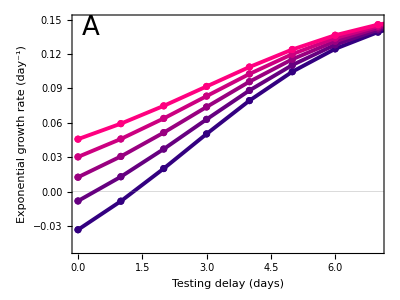

```mathematica
figure5a=Show[Show[Table[ListPlot[Transpose[{Table[k-1,{k,1,10}],growthrate[[7+2*j]]}],Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.2,0.0,0.5],Thickness[0.007]}],{j,1,numberlines}], PlotRange->{{0,7},{-0.05,0.15}},GridLines->{None,{{0,{Red,Thickness[0.007]}}}},PlotRange->{{1,10},All},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Testing delay (days)", "Exponential growth rate (day^-1)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["A",FontSize->26],{0.3,0.15*0.95}]]]
```

```mathematica
Table[Max[0.0,doubtime[[20,i]]],{i,1,Length[doubtime[[1]]]}]
```

{10.5247,9.03708,7.77352,6.73724,5.93787,5.35914,4.96219,4.70208,4.54157,4.45954}

```mathematica
doubtimepos=Transpose[Table[Table[If[doubtime[[j,k]]>0,doubtime[[j,k]],100],{j,1,Length[scenarioasymptomatic]}],{k,1,10}]];
```

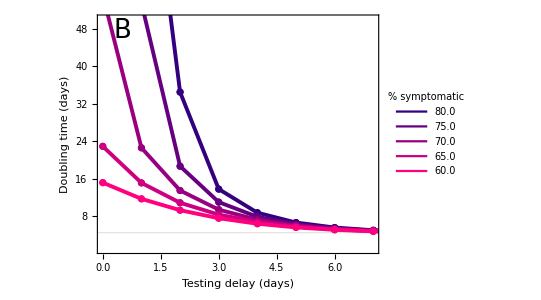

```mathematica
figure5b=Show[Show[Table[ListPlot[Transpose[{Table[k-1,{k,1,10}], doubtimepos[[7+2*j]]}],Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize, PlotStyle->{RGBColor[j*0.2,0.0,0.5],Thickness[0.007]}],{j,1,numberlines}],   PlotRange->{{0,7},{1,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Testing delay (days)", "Doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["B",FontSize->26],{0.5,50*0.95}]],Graphics[Inset[legendsymp,{5.5,35}]]]
```

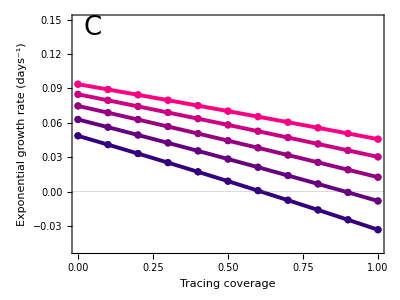

```mathematica
figure5c=Show[Show[Table[ListPlot[Transpose[{Table[(k-1)*0.1,{k,1,11}],growthrate2[[7+2*j]]}],Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.2,0.0,0.5],Thickness[0.007]}],{j,1,numberlines}],  GridLines->{None,{{0,{Red,Thickness[0.007]}}}},PlotRange->{{0,1},{-0.05,0.15}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Tracing coverage", "Exponential growth rate (days^-1)"},  (*PlotLabel->"Varying proportion asymptomatic", *)FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["C",FontSize->26],{0.05,0.15*0.95}]]]
```

```mathematica
doubtimepos2=Transpose[Table[Table[If[doubtime2[[j,k]]>0,doubtime2[[j,k]],100],{j,1,Length[scenarioasymptomatic]}],{k,1,11}]];
```

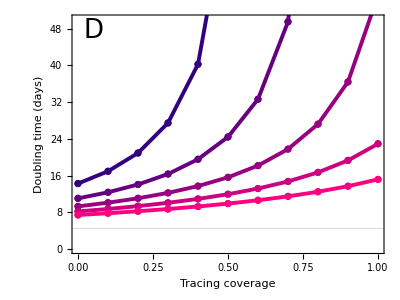

```mathematica
figure5d=Show[Show[Table[ListPlot[Transpose[{Table[(k-1)*0.1,{k,1,11}],doubtimepos2[[7+2*j]]}],Joined->True,Mesh->Full,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[j*0.2,0.0,0.5],Thickness[0.007]}],{j,1,numberlines}],   PlotRange->{{0,1},{0,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Tracing coverage", "Doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],Graphics[Text[StyleForm["D",FontSize->26],{0.0+0.05,50*0.95}]]]
```

## Scenarios reduced contact rate

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=1.0; coverage3=1.0;diagdelay=1;fractest=0.8;
```

```mathematica
progdiag=probdiagtest[fractest];
```

```mathematica
ydata000={};ydata111={};critcov222={};critcov333={};growthrate3={};doubtime3={};
growthrate4={};growthrate5={};
doubtime4={};doubtime5={};reffredcontact={}; 
scenarios=Length[scenariocontactred];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[9]]; 
 probsymp=factorasymptomatic*probsympdata;
probdevelopingsymptoms=Table[Max[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],0],{i,1,infectious}];fraccas=Total[probdevelopingsymptoms];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
contactreduction1=1.0;contactreduction2=1.0;mu1=meanhouseholdcontacts*saturation1*contactreduction1;mu2=negbinn*saturation2*contactreduction2 ;transmissibility=0.1211;
 For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}]; 
xdata4=Table[{pt,rzero[pt]},{pt,0.01,0.5,0.001}];
xvalues2=Table[Take[Flatten[Position[xdata4[[All,2]],SelectFirst [xdata4[[All,2]], #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}];
xdata4[[xvalues2]];
```

```mathematica
xdata4;
```

```mathematica
xvalues2
```

{82,112,143,173,204}

```mathematica
Table[rzero[xdata4[[xvalues2]][[i,1]]],{i,1,5}]
```

{1.49512,1.98802,2.49734,2.99024,3.49956}

```mathematica
Do[transmissibility=xdata4[[xvalues2]][[n,1]]; Do[ contactreduction1=scenariocontactred[[1]];contactreduction2=scenariocontactred[[l]];mu1=meanhouseholdcontacts*saturation1*contactreduction1;
mu2=negbinn*saturation2*contactreduction2 ;
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];  pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];reffredcontact=Append[reffredcontact,rzero[transmissibility]];critcov222=Append[critcov222,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,vaccdelay3,cv1,0,j,fractiontrace]==1, {cv1,0.5}],1,2],{j,diagdelay,diagdelay}]];critcov333=Append[critcov333,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,j,coverage2,cv2,diagdelay,fractiontrace]==1, {cv2,0.5}],1,2],{j,diagdelay,diagdelay}]];growthrate3=Append[growthrate3,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,7}]]; doubtime3=Append[doubtime3,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,7}]];
growthrate4=Append[growthrate4,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.2,diagdelay,fractiontrace],{cv,1,6}]];growthrate5=Append[growthrate5,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.2,0.0,diagdelay,fractiontrace],{cv,1,6}]];
doubtime4=Append[doubtime4,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.2,diagdelay,fractiontrace],{cv,1,6}]];doubtime5=Append[doubtime5,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.2,0.0,diagdelay,fractiontrace],{cv,1,6}]],{l,1,Length[scenariocontactred]}],{n,1,5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
reffredcontact;
```

```mathematica
xvalues2
```

{82,112,143,173,204}

```mathematica
legendtext=Table[ToString[Ceiling[100*scenariocontactred[[i]]]],{i,1,Length[scenariocontactred]}];
```

```mathematica
coverageshousehold=Table[Table[{scenariocontactred[[j]],Max[-1.0,Min[2.0,critcov222[[(k-1)*Length[scenariocontactred]+j]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

```mathematica
legend4={LineLegend[ Table[RGBColor[k 0.2,0.5,0.0],{k,1,5}],coverageshousehold[[All,1,3]],LegendLabel->"R_0",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

```mathematica
figure7aold=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverageshousehold[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True,(*Mesh->Full,*)AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.5,0.0], Thickness[0.007]}, PlotLegends->Placed[legend4[[k]],{0.1,0.35}], Frame->True,FrameStyle->Directive[Black,17],GridLines->{None,{1.0}},FrameLabel->{"Reduction non-household contacts (%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]],Graphics[Text[StyleForm["A",FontSize->26],{100-5,1.0*0.95}]],Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]];
```

```mathematica
coverages=Table[Table[{scenariocontactred[[j]],Max[-1.0,Min[2.0,critcov333[[(k-1)*Length[scenariocontactred]+j,1]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

```mathematica
reffredcontact;
```

```mathematica
scenarios
```

20

```mathematica
figure7bold=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverages[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True,(*Mesh->Full,*)AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, PlotLegends->Placed[legend[[k]],{0.9,0.4}], Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts(%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,1,5}]],Graphics[Text[StyleForm["B",FontSize->26],{100-5,1.0*0.95}]],Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]];
```

```mathematica
growthrate3[[2]]
```

{-0.0814191,-0.0634205,-0.0427534,-0.020526,0.00129226,0.0206379,0.0361841}

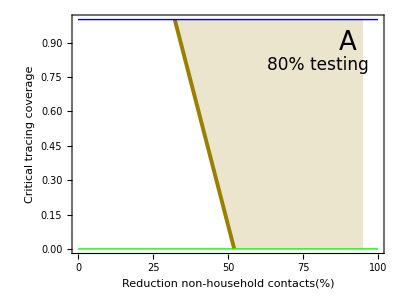

```mathematica
figure9a=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverageshousehold[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,Filling->1.0,PlotStyle->{RGBColor[k 0.2,0.5,0.0], Thickness[0.007]}, (*PlotLegends->Placed["household",{0.45,0.8}],*) Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts(%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}]],Graphics[Text[StyleForm["A",FontSize->26],{90,1.0*0.90}]],Graphics[Text[Style["80% testing",Directive[Black,17]],{80,0.8}]],Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]]
```

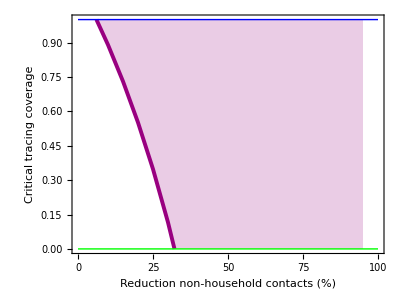

```mathematica
figure9b=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverages[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True, AspectRatio->AspRat,ImageSize->ImSize,Filling->1.0,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, (*PlotLegends->Placed["non-household",{0.2,0.2}], *)Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}]](*,Graphics[Text[StyleForm["A",FontSize->26],{100-5,1.0*0.95}]]*),  Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]]
```

```mathematica
legendcontacts=SwatchLegend[ {RGBColor[0.6,0.5,0.0],RGBColor[ 0.6,0.0,0.5]},{"household contacts","all contacts" },LegendLabel->"Required tracing for control", LabelStyle->Directive[Black,17], LegendMargins->5]
```

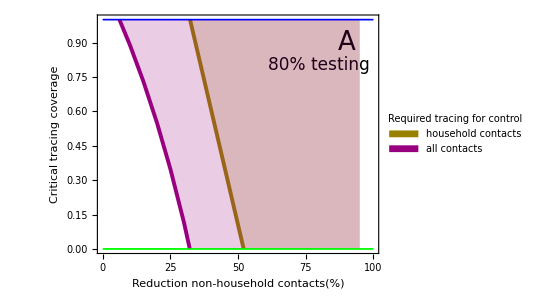

```mathematica
figuretracing=Legended[Show[figure9a,figure9b],legendcontacts]
```

```mathematica
table2[doublepairs_]:=TableForm[TableForm[doublepairs, TableDepth->2,TableAlignments->Center]]
```

```mathematica
LineLegend[Table[RGBColor[i*0.2,0.5,0.0],{i,1,6}],Table[(i-1)*20,{i,1,6}],LegendLabel->"Tracing coverage(%)",LabelStyle->Directive[Black,10], LegendMargins->5,LegendLayout->table2]
```

```mathematica
legendgrowthrate=TableForm[{LineLegend[Table[RGBColor[i*0.2,0.5,0.0],{i,1,6}],Table[(i-1)*20,{i,1,6}],LegendLabel->"Coverage household contacts (%)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table2],LineLegend[Table[RGBColor[i*0.2,0.0,0.5],{i,1,6}],Table[(i-1)*20,{i,1,6}],LegendLabel->"Coverage non-household contacts(%)",LabelStyle->Directive[Black,17], LegendMargins->5,LegendLayout->table2]},TableDirections->Row,TableHeadings->{"Household contacts","Non-household| contacts"}]
```

|

```mathematica
figure7aa=Show[Show[Table[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,growthrate5[[(k-1)*scenarios+j,i]]},{j,1,scenarios}],PlotRange->{{0,100},{-0.07,0.07}},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i 0.2,0.5,0.0], Thickness[0.007]}, Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)","growth rate (days^-1)"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}],{i,1,6}]],Graphics[Text[StyleForm["A",FontSize->26],{85,0.06*0.85}]]];
```

```mathematica
figure7ab=Show[Show[Table[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,growthrate4[[(k-1)*scenarios+j,i]]},{j,1,scenarios}],PlotRange->{{0,100},{-0.07,0.07}},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i 0.2,0.0,0.5], Thickness[0.007]}, Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)","growth rate (days^-1)"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}],{i,1,6}]](*,Graphics[Text[StyleForm["A",FontSize->26],{5,0.1*0.85}]]*)];
```

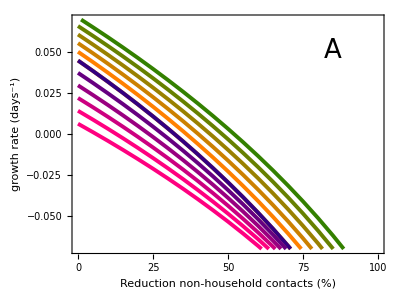

```mathematica
figure7a=Show[figure7aa,figure7ab]
```

```mathematica
doubtime3;
```

```mathematica
figure7ac=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,If[doubtime4[[3*scenarios+j,i]]>0,doubtime4[[3*scenarios+j,i]],70]},{j,1,scenarios}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i*0.2,0.0,0.5],Thickness[0.007]},   PlotRange->{{0,100},{0,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],{i,1,6}],Graphics[Text[StyleForm["B",FontSize->26],{95,50*0.9}]]]];
```

```mathematica
figure7ad=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100,If[doubtime5[[3*scenarios+j,i]]>0,doubtime5[[3*scenarios+j,i]],70]},{j,1,scenarios}],Joined->True,AspectRatio->AspRat,ImageSize->ImSize,PlotStyle->{RGBColor[i*0.2,0.5,0.0],Thickness[0.007]},   PlotRange->{{0,100},{0,50}},GridLines->{None,{{unconstraineddoubtime,{Blue,Thickness[0.007]}}}},Frame->True, FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)", "doubling time (days)"},  (*PlotLabel->"Varying proportion asymptomatic",*) FrameTicks->{Automatic, Automatic, None, None}],{i,1,6}](*,Graphics[Text[StyleForm["D",FontSize->26],{0.0+0.05,50*0.95}]]*)]];
```

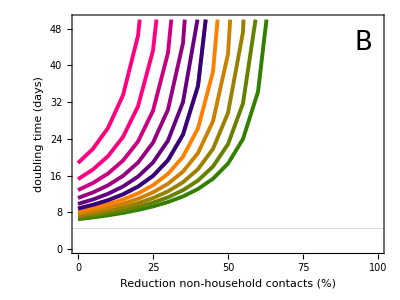

```mathematica
figure7b=Show[figure7ad,figure7ac]
```

## Scenario with 60% testing rate

```mathematica
vaccdelay2=1.0;vaccdelay3=1.0;coverage2=1.0; coverage3=1.0;diagdelay=1;fractest=0.6;
```

```mathematica
progdiag=probdiagtest[fractest];
```

```mathematica
ydata000={};ydata111={};critcov222={};critcov333={};growthrate3={};doubtime3={};
growthrate4={};growthrate5={};
doubtime4={};doubtime5={};reffredcontact={}; 
scenarios=Length[scenariocontactred];
```

```mathematica
factorasymptomatic=scenarioasymptomatic[[9]]; 
 probsymp=factorasymptomatic*probsympdata;
probdevelopingsymptoms=Table[Max[Product[(1-probsymp[[j-1]]),{j,2,i}]*probsymp[[i]],0],{i,1,infectious}];fraccas=Total[probdevelopingsymptoms];pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];
```

```mathematica
contactreduction1=1.0;contactreduction2=1.0;mu1=meanhouseholdcontacts*saturation1*contactreduction1;mu2=negbinn*saturation2*contactreduction2 ;transmissibility=0.1211;
 For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}]; 
xdata4=Table[{pt,rzero[pt]},{pt,0.01,0.5,0.001}];
xvalues2=Table[Take[Flatten[Position[xdata4[[All,2]],SelectFirst [xdata4[[All,2]], #>1.0+k*0.5&]]-1],1] [[1]],{k,1,5}];
xdata4[[xvalues2]];
```

```mathematica
xdata4;
```

```mathematica
xvalues2
```

{82,112,143,173,204}

```mathematica
Table[rzero[xdata4[[xvalues2]][[i,1]]],{i,1,5}]
```

{1.49512,1.98802,2.49734,2.99024,3.49956}

```mathematica
Do[transmissibility=xdata4[[xvalues2]][[n,1]]; Do[ contactreduction1=scenariocontactred[[1]];contactreduction2=scenariocontactred[[l]];mu1=meanhouseholdcontacts*saturation1*contactreduction1;
mu2=negbinn*saturation2*contactreduction2 ;
For [i=1,i≤infectious,i++,{contactdist1[[i]]=PoissonDistribution[mu1[[i]]];contactdist2[[i]]=NegativeBinomialDistribution[mu2[[i]],negbinp]}];  pd=Table[Table[Prepend[Table[( ∏_(k=j+1)^(i-1) (1-probdiag[[ds,k]])) probdiag[[ds,i]], {i,j+2,infectious}], probdiag[[ds,j+1]]],{j,1,infectious-1}],{ds,1,infectious}];reffredcontact=Append[reffredcontact,rzero[transmissibility]];critcov222=Append[critcov222,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,vaccdelay3,cv1,0,j,fractiontrace]==1, {cv1,0.5}],1,2],{j,diagdelay,diagdelay}]];critcov333=Append[critcov333,Table[Part[FindRoot[reffvacc[transmissibility,vaccdelay2,j,coverage2,cv2,diagdelay,fractiontrace]==1, {cv2,0.5}],1,2],{j,diagdelay,diagdelay}]];growthrate3=Append[growthrate3,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,7}]]; doubtime3=Append[doubtime3,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,coverage3,dd,fractiontrace],{dd,1,7}]];
growthrate4=Append[growthrate4,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.2,diagdelay,fractiontrace],{cv,1,6}]];growthrate5=Append[growthrate5,Table[expgrowtheff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.2,0.0,diagdelay,fractiontrace],{cv,1,6}]];
doubtime4=Append[doubtime4,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,coverage2,(cv-1)*0.2,diagdelay,fractiontrace],{cv,1,6}]];doubtime5=Append[doubtime5,Table[doublingtimeeff[transmissibility,vaccdelay2,vaccdelay3,(cv-1)*0.2,0.0,diagdelay,fractiontrace],{cv,1,6}]],{l,1,Length[scenariocontactred]}],{n,1,5}]
```

```mathematica
reffredcontact;
```

```mathematica
xvalues2
```

{82,112,143,173,204}

```mathematica
legendtext=Table[ToString[Ceiling[100*scenariocontactred[[i]]]],{i,1,Length[scenariocontactred]}];
```

```mathematica
coverageshousehold=Table[Table[{scenariocontactred[[j]],Max[-1.0,Min[2.0,critcov222[[(k-1)*Length[scenariocontactred]+j]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

```mathematica
legend4={LineLegend[ Table[RGBColor[k 0.2,0.5,0.0],{k,1,5}],coverageshousehold[[All,1,3]],LegendLabel->"R_0",LabelStyle->Directive[Black,14], LegendMargins->5],None,None,None,None};
```

```mathematica
coverages=Table[Table[{scenariocontactred[[j]],Max[-1.0,Min[2.0,critcov333[[(k-1)*Length[scenariocontactred]+j,1]]]],NumberForm[1.0+0.5*k,{2,1}]},{j,1,Length[scenariocontactred]}],{k,1,5}];
```

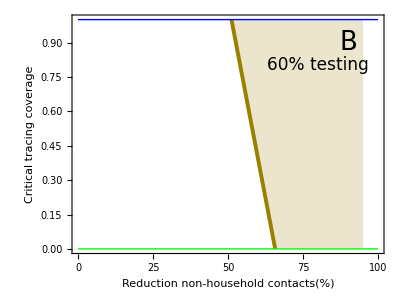

```mathematica
figure10a=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverageshousehold[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True,AspectRatio->AspRat,ImageSize->ImSize,Filling->1.0,PlotStyle->{RGBColor[k 0.2,0.5,0.0], Thickness[0.007]}, (*PlotLegends->Placed["household",{0.45,0.8}],*) Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts(%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}]],Graphics[Text[StyleForm["B",FontSize->26],{90,1.0*0.90}]],Graphics[Text[Style["60% testing",Directive[Black,17]],{80,0.8}]],Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]]
```

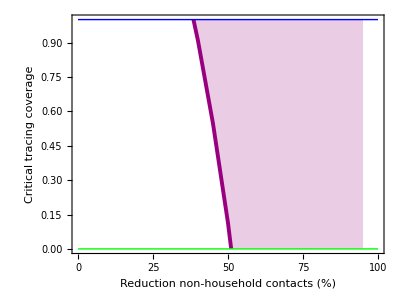

```mathematica
figure10b=Show[Show[Table[ListPlot[ Table[{(1-scenariocontactred[[j]])*100, coverages[[k,j,2]]},{j,1,scenarios}],PlotRange->{{0,100},{0,1.0}},PlotRangePadding->{None,0.05},Joined->True, AspectRatio->AspRat,ImageSize->ImSize,Filling->1.0,PlotStyle->{RGBColor[k 0.2,0.0,0.5], Thickness[0.007]}, (*PlotLegends->Placed["non-household",{0.2,0.2}], *)Frame->True,FrameStyle->Directive[Black,17],FrameLabel->{"Reduction non-household contacts (%)","Critical tracing coverage"}, FrameTicks->{{Automatic, None}, {Automatic,None}} ],{k,3,3}]](*,Graphics[Text[StyleForm["B",FontSize->26],{100-5,1.0*0.95}]]*),  Graphics[{Blue,Thick,Line[{{0,1},{100,1}}]}],Graphics[{Green,Thick,Line[{{0,0},{100,0}}]}]]
```

```mathematica
legendcontacts=SwatchLegend[ {RGBColor[0.6,0.5,0.0],RGBColor[ 0.6,0.0,0.5]},{"household contacts","all contacts" },LegendLabel->"Required tracing for control", LabelStyle->Directive[Black,17], LegendMargins->5]
```

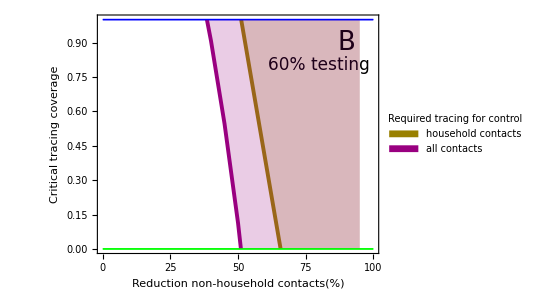

```mathematica
figuretracing2=Legended[Show[figure10a,figure10b],legendcontacts]
```

## Output

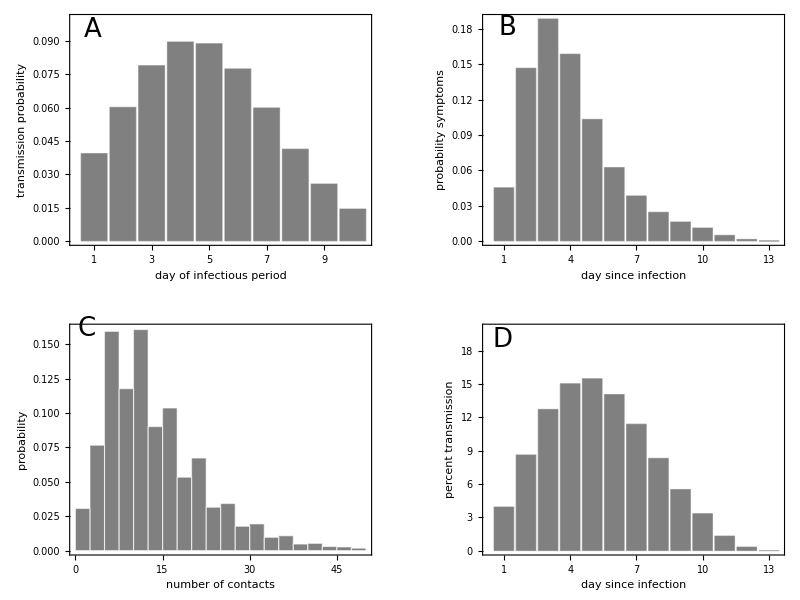

```mathematica
figure1=Show[GraphicsGrid[{{figure1a,figure1b},{figure1c,figure1d2}},ImageSize->2*ImSize]]
```

```mathematica
Export[StringJoin[filepath,"Figure_1_",date,".pdf"],figure1,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_1_",date,".eps"],figure1,"eps"];
```

```mathematica
figure2A=Show[Legended[figure2a,legendr0]]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure_2A_",date,".pdf"],figure2A,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_2A_",date,".eps"],figure2A,"eps"];
```

```mathematica
figure2B=Show[Legended[figure2b,legendr02]]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure_2B_",date,".pdf"],figure2B,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_2B_",date,".eps"],figure2B,"eps"];
```

```mathematica
figure3A=Show[figure3firstpanel,ImageSize->2*ImSize]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure_3A_",date,".pdf"],figure3A,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_3A_",date,".eps"],figure3A,"eps"];
```

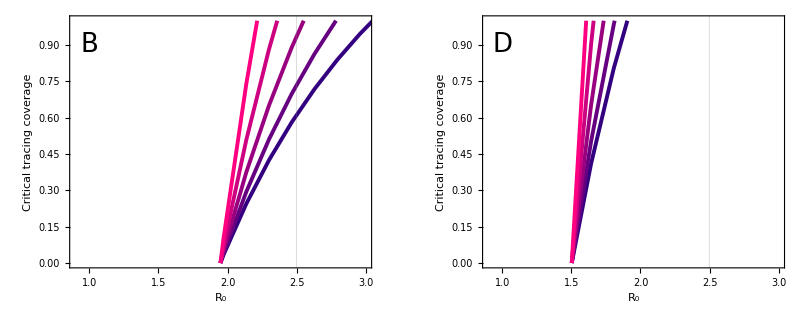

```mathematica
figure3B=Show[figure3secondpanel,ImageSize->2*ImSize]
```

```mathematica
Export[StringJoin[filepath,"Figure_3B_",date,".pdf"],figure3B,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_3B_",date,".eps"],figure3B,"eps"];
```

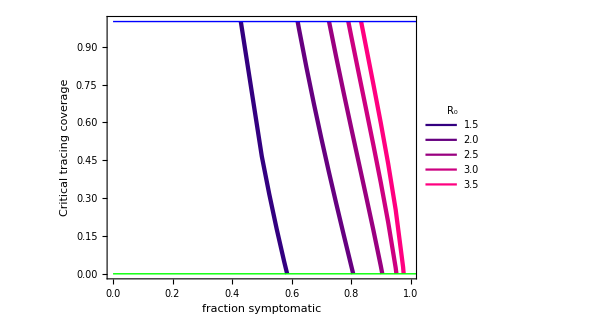

```mathematica
figure4=Show[figure4a,ImageSize->1.1*ImSize]
```

```mathematica
Export[StringJoin[filepath,"Figure_4_",date,".pdf"],figure4,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_4_",date,".eps"],figure4,"eps"];
```

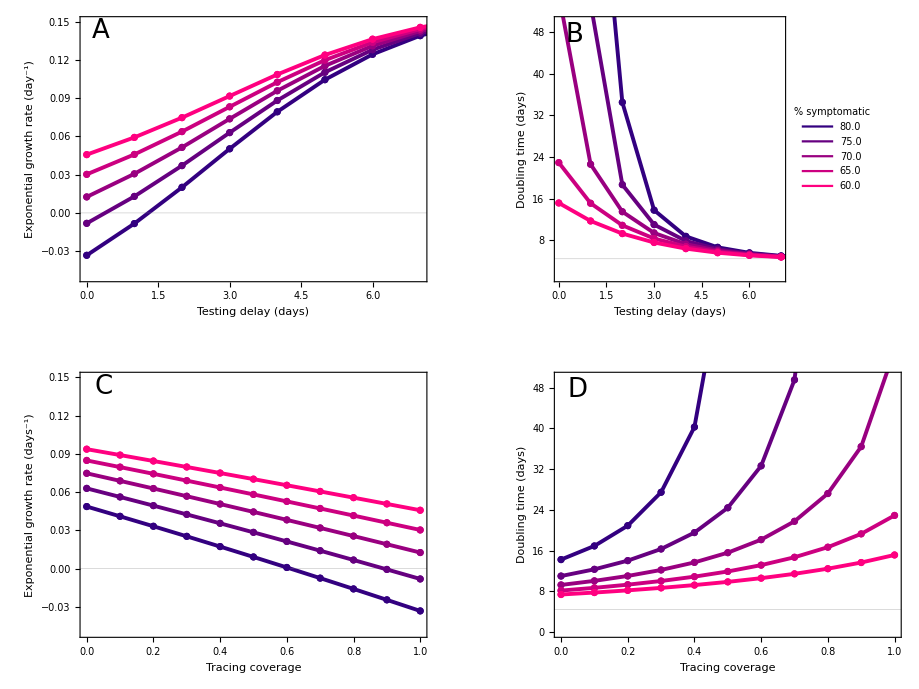

```mathematica
figure5=Show[Show[GraphicsGrid[{{figure5a,figure5b},{figure5c,figure5d}},ImageSize->2.3*ImSize]](*,PlotLabel->"Varying proportion asymptomatic"*)]
```

```mathematica
Export[StringJoin[filepath,"Figure_5_",date,".pdf"],figure5,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_5_",date,".eps"],figure5,"eps"];
```

```mathematica
figure6A=Show[figuretracing, ImageSize->1.0ImSize,FrameStyle->Directive[Black,17]]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure_6A_",date,".pdf"],figure6A,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_6A_",date,".eps"],figure6A,"eps"];
```

```mathematica
figure6B=Show[figuretracing2, ImageSize->1.0ImSize,FrameStyle->Directive[Black,17]]
```

-Graphics-

```mathematica
Export[StringJoin[filepath,"Figure_6B_",date,".pdf"],figure6B,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_6B_",date,".eps"],figure6B,"eps"];
```

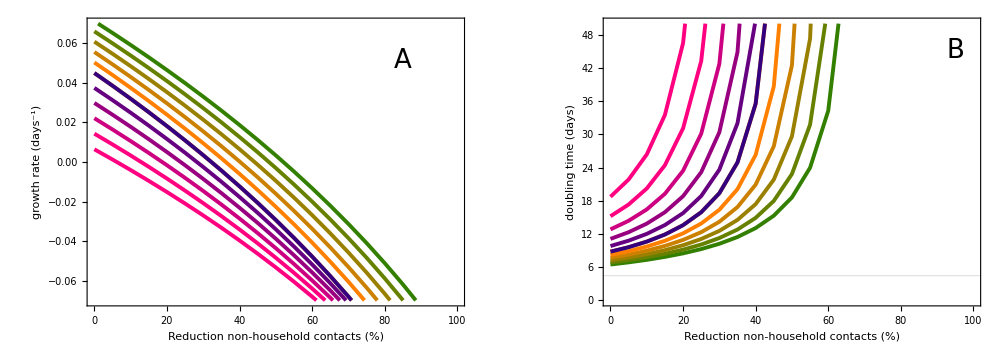

```mathematica
figure7=Legended[Show[GraphicsRow[{figure7a,figure7b},ImageSize->2.5*ImSize]],Placed[legendgrowthrate,Bottom]]
```

```mathematica
Export[StringJoin[filepath,"Figure_7_",date,".pdf"],figure7,"pdf"];
```

```mathematica
Export[StringJoin[filepath,"Figure_7_",date,".eps"],figure7,"eps"];
```